## Construcción de Spline’s

```mathematica
datos={{834.676,1291.97},{884.756,1308.67},{916.057,1337.88},{953.617,1415.09},{970.311,1523.6},{1003.7,1607.06},{1035.,1652.97},{1097.6,1694.71},{1164.37,1711.4},{1247.84,1713.49},{1322.96,1698.88},{1385.56,1673.84},{1427.3,1634.19},{1485.72,1506.9},{1460.68,1565.33},{1525.37,1452.65},{1579.62,1415.09},{1673.53,1415.09},{1744.47,1431.78},{1819.59,1450.56},{1907.23,1477.69},{1976.1,1519.42},{2017.83,1573.68},{2038.7,1642.54}};
```

```mathematica
Dimensions[datos]
```

{24,2}

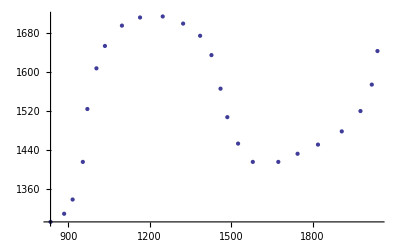

```mathematica
ListPlot[datos]
```

```mathematica
datos[[1,2]]
```

1291.97

```mathematica
a[n_]:=datos[[n+1,2]]
```

```mathematica
a[0]
```

1291.97

```mathematica
x[n_]:=datos[[n+1,1]]
```

```mathematica
x[0]
```

834.676

```mathematica
Clear[h]
```

```mathematica
h[j_]:=x[j+1]-x[j];
```

```mathematica
h[0]
```

50.08

```mathematica
x[0]
```

834.676

```mathematica
x[1]-x[0]
```

50.08

```mathematica
m=({{h[0], 2 (h[0]+h[1]), h[1], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, h[1], 2 (h[1]+h[2]), h[2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, h[2], 2 (h[2]+h[3]), h[3], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, h[3], 2 (h[3]+h[4]), h[4], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, h[4], 2 (h[4]+h[5]), h[5], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, h[5], 2 (h[5]+h[6]), h[6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, h[6], 2 (h[6]+h[7]), h[7], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, h[7], 2 (h[7]+h[8]), h[8], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, h[8], 2 (h[8]+h[9]), h[9], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, h[9], 2 (h[9]+h[10]), h[10], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[10], 2 (h[10]+h[11]), h[11], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[11], 2 (h[11]+h[12]), h[12], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[12], 2 (h[12]+h[13]), h[13], 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[13], 2 (h[13]+h[14]), h[14], 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[14], 2 (h[14]+h[15]), h[15], 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[15], 2 (h[15]+h[16]), h[16], 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[16], 2 (h[16]+h[17]), h[17], 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[17], 2 (h[17]+h[18]), h[18], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[18], 2 (h[18]+h[19]), h[19], 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[19], 2 (h[19]+h[20]), h[20], 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[20], 2 (h[20]+h[21]), h[21], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, h[21], 2 (h[21]+h[22]), h[22]}});
```

```mathematica
h[0]
```

50.08

```mathematica
h[22]
```

20.87

```mathematica
m//Dimensions
```

{22,24}

```mathematica
r=Table[3/h[j-1](a[j-1]-a[j])+3/h[j](a[j+1]-a[j]),{j,1,22}];
```

```mathematica
results=LinearSolve[m,r]
```

{0.0106538,0.011612,-0.0199462,0.153112,-0.151663,0.0190028,-0.0157579,-0.000566494,-0.00175851,-0.00130046,-0.00132214,-0.00247079,-0.0251896,0.0250302,0.0264859,0.00465739,0.00603161,0.000395061,0.000128664,-0.000285126,0.00298761,-0.000306484,0.0466105,0.00837494}

```mathematica
c[0]
```

0.0106538

```mathematica
d[0]
```

6.37778×10^-6

```mathematica
d[22]
```

-0.000610694

```mathematica
b[0]
```

-0.21607

```mathematica
f[t_]:=Piecewise[Table[{a[i]+b[i](t-x[i])+c[i](t-x[i])^2+d[i](t-x[i])^3,x[i]<t<x[i+1]},{i,0,22}]]
```

```mathematica
f[t]
```

Piecewise[{{1291.97-0.21607 (-834.676+t)+0.0106538 (-834.676+t)^2+6.37778×10^-6 (-834.676+t)^3, 834.676<t<884.756}, {1308.67+0.898998 (-884.756+t)+0.011612 (-884.756+t)^2-0.000336072 (-884.756+t)^3, 884.756<t<916.057}, {1337.88+0.638129 (-916.057+t)-0.0199462 (-916.057+t)^2+0.00153584 (-916.057+t)^3, 916.057<t<953.617}, {1415.09+5.63985 (-953.617+t)+0.153112 (-953.617+t)^2-0.00608553 (-953.617+t)^3, 953.617<t<970.311}, {1523.6+5.66405 (-970.311+t)-0.151663 (-970.311+t)^2+0.00170381 (-970.311+t)^3, 970.311<t<1003.7}, {1607.06+1.23466 (-1003.7+t)+0.0190028 (-1003.7+t)^2-0.000370188 (-1003.7+t)^3, 1003.7<t<1035.}, {1652.97+1.33622 (-1035.+t)-0.0157579 (-1035.+t)^2+0.0000808912 (-1035.+t)^3, 1035.<t<1097.6}, {1694.71+0.314318 (-1097.6+t)-0.000566494 (-1097.6+t)^2-5.95084×10^-6 (-1097.6+t)^3, 1097.6<t<1164.37}, {1711.4+0.159077 (-1164.37+t)-0.00175851 (-1164.37+t)^2+1.82917×10^-6 (-1164.37+t)^3, 1164.37<t<1247.84}, {1713.49-0.0962551 (-1247.84+t)-0.00130046 (-1247.84+t)^2-9.61981×10^-8 (-1247.84+t)^3, 1247.84<t<1322.96}, {1698.88-0.293265 (-1322.96+t)-0.00132214 (-1322.96+t)^2-6.11633×10^-6 (-1322.96+t)^3, 1322.96<t<1385.56}, {1673.84-0.530703 (-1385.56+t)-0.00247079 (-1385.56+t)^2-0.000181431 (-1385.56+t)^3, 1385.56<t<1427.3}, {1634.19-1.68525 (-1427.3+t)-0.0251896 (-1427.3+t)^2+0.000286544 (-1427.3+t)^3, 1427.3<t<1485.72}, {1565.33-2.98452 (-1460.68+t)+0.0264859 (-1460.68+t)^2-0.000112478 (-1460.68+t)^3, 1460.68<t<1525.37}, {1452.65-0.969864 (-1525.37+t)+0.00465739 (-1525.37+t)^2+8.44379×10^-6 (-1525.37+t)^3, 1525.37<t<1579.62}, {1415.09-0.389986 (-1579.62+t)+0.00603161 (-1579.62+t)^2-0.0000200069 (-1579.62+t)^3, 1579.62<t<1673.53}, {1415.09+0.213543 (-1673.53+t)+0.000395061 (-1673.53+t)^2-1.25175×10^-6 (-1673.53+t)^3, 1673.53<t<1744.47}, {1431.78+0.250696 (-1744.47+t)+0.000128664 (-1744.47+t)^2-1.83613×10^-6 (-1744.47+t)^3, 1744.47<t<1819.59}, {1450.56+0.238943 (-1819.59+t)-0.000285126 (-1819.59+t)^2+0.0000124477 (-1819.59+t)^3, 1819.59<t<1907.23}, {1477.69+0.475789 (-1907.23+t)+0.00298761 (-1907.23+t)^2-0.0000159436 (-1907.23+t)^3, 1907.23<t<1976.1}, {1519.42+0.660438 (-1976.1+t)-0.000306484 (-1976.1+t)^2+0.000374766 (-1976.1+t)^3, 1976.1<t<2017.83}, {1573.68+2.5927 (-2017.83+t)+0.0466105 (-2017.83+t)^2-0.000610694 (-2017.83+t)^3, 2017.83<t<2038.7}, {0, True}}]

```mathematica
funcion[t_]:=Piecewise[{{1291.97-0.2160697773793908 (-834.676+t)+0.01065376849164662 (-834.676+t)^2+6.377776783923537*^-6 (-834.676+t)^3, 834.676<t<884.756}, {1308.67+0.8989981897194892 (-884.756+t)+0.011611965675663291 (-884.756+t)^2-0.0003360718864517504 (-884.756+t)^3, 884.756<t<916.057}, {1337.88+0.6381285503251215 (-916.057+t)-0.019946192677815472 (-916.057+t)^2+0.001535842084048586 (-916.057+t)^3, 916.057<t<953.617}, {1415.09+5.63985480367674 (-953.617+t)+0.15311249335277893 (-953.617+t)^2-0.006085531897817575 (-953.617+t)^3, 953.617<t<970.311}, {1523.6+5.664050723331793 (-970.311+t)-0.15166311515372222 (-970.311+t)^2+0.0017038136988473953 (-970.311+t)^3, 970.311<t<1003.7}, {1607.06+1.234655180821764 (-1003.7+t)+0.019002791618724854 (-1003.7+t)^2-0.0003701879120421258 (-1003.7+t)^3, 1003.7<t<1035.}, {1652.97+1.336221749508283 (-1035.+t)-0.01575785332203071 (-1035.+t)^2+0.00008089115725130834 (-1035.+t)^3, 1035.<t<1097.6}, {1694.71+0.3143176077604506 (-1097.6+t)-0.0005664939902350272 (-1097.6+t)^2-5.950843437858822*^-6 (-1097.6+t)^3, 1097.6<t<1164.37}, {1711.4+0.1590772623122276 (-1164.37+t)-0.0017585074392725275 (-1164.37+t)^2+1.8291731219702733*^-6 (-1164.37+t)^3, 1164.37<t<1247.84}, {1713.49-0.09625510023422014 (-1247.84+t)-0.0013004641977999512 (-1247.84+t)^2-9.619807428092417*^-8 (-1247.84+t)^3, 1247.84<t<1322.96}, {1698.88-0.29326538266694907 (-1322.96+t)-0.0013221433958199003 (-1322.96+t)^2-6.1163329100860945*^-6 (-1322.96+t)^3, 1322.96<t<1385.56}, {1673.84-0.5307030580877894 (-1385.56+t)-0.002470790716334067 (-1385.56+t)^2-0.00018143109655121276 (-1385.56+t)^3, 1385.56<t<1427.3}, {1634.19-1.6852474588167188 (-1427.3+t)-0.025189592626476933 (-1427.3+t)^2+0.0002865444035074945 (-1427.3+t)^3, 1427.3<t<1485.72}, {1565.33-2.9845229219715974 (-1460.68+t)+0.02648589675329438 (-1460.68+t)^2-0.00011247751467940528 (-1460.68+t)^3, 1460.68<t<1525.37}, {1452.65-0.9698639943345785 (-1525.37+t)+0.004657385479462256 (-1525.37+t)^2+8.44378998373338*^-6 (-1525.37+t)^3, 1525.37<t<1579.62}, {1415.09-0.3899858648359202 (-1579.62+t)+0.006031612299314864 (-1579.62+t)^2-0.00002000692636155192 (-1579.62+t)^3, 1579.62<t<1673.53}, {1415.09+0.21354301864317776 (-1673.53+t)+0.00039506093547483564 (-1673.53+t)^2-1.2517477042809679*^-6 (-1673.53+t)^3, 1673.53<t<1744.47}, {1431.78+0.2506960647889504 (-1744.47+t)+0.00012866398904975984 (-1744.47+t)^2-1.8361292231273346*^-6 (-1744.47+t)^3, 1744.47<t<1819.59}, {1450.56+0.2389426315646801 (-1819.59+t)-0.00028512609267421565 (-1819.59+t)^2+0.00001244766710671554 (-1819.59+t)^3, 1819.59<t<1907.23}, {1477.69+0.4757887193532874 (-1907.23+t)+0.0029876145430234383 (-1907.23+t)^2-0.000015943559318498946 (-1907.23+t)^3, 1907.23<t<1976.1}, {1519.42+0.6604381627872802 (-1976.1+t)-0.00030648424777162363 (-1976.1+t)^2+0.0003747660991389412 (-1976.1+t)^3, 1976.1<t<2017.83}, {1573.68+2.592704060072005 (-2017.83+t)+0.046610483703432445 (-2017.83+t)^2-0.0006106938664393218 (-2017.83+t)^3, 2017.83<t<2038.7}, {0, True}}]
```

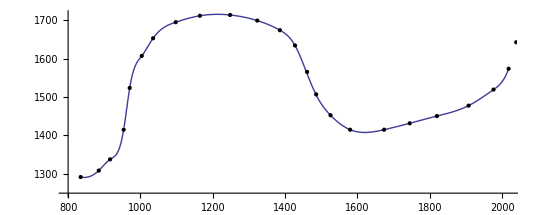

```mathematica
Plot[funcion[t],{t,x[0],x[22]},AspectRatio->Automatic,Epilog->Map[Point,datos],AxesOrigin->{800,1250}]
```